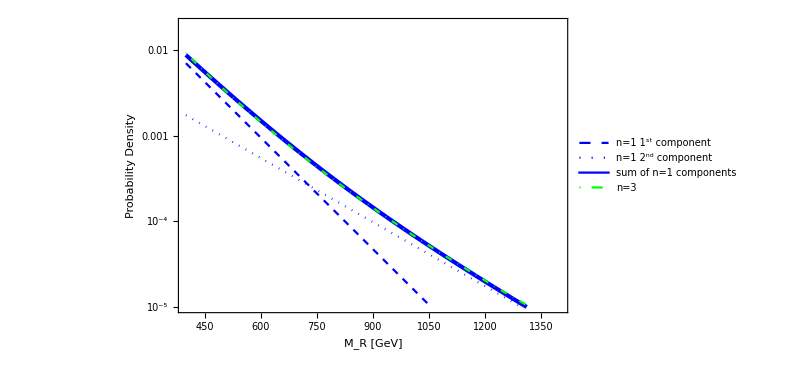

```mathematica
f1Dinf[b_,x0_,y0_,x_,n_,ymin_]:=-ⅇ^(-b n (-(x-x0) (-ymin+y0))^(1/n)) (-ymin+y0)
f1Dinf2[b_,x0_,y0_,x_,ymin_]:=-ⅇ^(-b  (-(x-x0) (-ymin+y0))) (-ymin+y0)
f=0.3;
lp = LogPlot[{(1-f)*f1Dinf2[0.02,-300,-0.25,x,0.25]/Integrate[f1Dinf2[0.02,-300,-0.25,xp,0.25],{xp,400,1400}]+f*f1Dinf2[0.0115,-300,-0.25,x,0.25]/Integrate[f1Dinf2[0.0115,-300,-0.25,xp,0.25],{xp,400,1400}],(1-f)*f1Dinf2[0.02,-300,-0.25,x,0.25]/Integrate[f1Dinf2[0.02,-300,-0.25,xp,0.25],{xp,400,1400}],f*f1Dinf2[0.0115,-300,-0.25,x,0.25]/Integrate[f1Dinf2[0.0115,-300,-0.25,xp,0.25],{xp,400,1400}],
f1Dinf[1.0,-300,-0.25,x,3.0,0.25]/Integrate[f1Dinf[1.0,-300,-0.25,xp,3.0,0.25],{xp,400,1400}]},{x,400,1500},PlotRange->{{400,1400},{10^(-5),0.02}},PlotStyle->{{Blue,Thickness[0.005]},{Blue,Dashed},{Blue,Dotted},{Green,DotDashed}},
AxesStyle->Black,TicksStyle->Black,AxesLabel->{Style["M_R",FontSize->24,FontFamily->"Helvetica",Black],Style["Probability Density",FontSize->24,FontFamily->"Helvetica"]},LabelStyle->Directive[FontSize->20,FontFamily->"Helvetica",Black],PlotLegends->Placed[LineLegend[{{Blue,Dashed},{Blue,Dotted},Blue,{Green,DotDashed}},{"n=1 1^st component","n=1 2^nd component","sum of n=1 components","n=3"}],{Scaled[{0.9,0.9}],{0.9,0.8}}],ImageSize->{600,500}];
Show[lp,Frame->True,FrameLabel->{{"Probability Density",""},{"M_R [GeV]",""}}]
```